## Setup

```mathematica
<<MaTeX`
SetDirectory[NotebookDirectory[]]
```

/home/lucas/phd-thesis/img/wave_scattering

## Functions

```mathematica
ClearAll[texStyle,texStyle14];
texStyle[x_]:={FontFamily->"TeX Gyre Pagella",FontSize->x,GrayLevel[0]};
texStyle14=texStyle[14];

ClearAll[A];
A[l_,m_]:=(-1)^m Sqrt[(2 l+1)/(4 π) (l-m)!/(l+m)!];

ClearAll[baseGaussian];
baseGaussian[x_,sigma_]:=Exp[-1/2*(x/sigma)^2];

ClearAll[exactGaussian];
exactGaussian[x_,t_,sigma_]:=(baseGaussian[x-t,sigma]-baseGaussian[x+t,sigma])/x;
```

## Pallete

```mathematica
(*https://github.com/matplotlib/matplotlib/blob/06567e021f21be046b6d6dcf00380c1cb9adaf3c/lib/matplotlib/_cm.py*)
ClearAll[toPallete];
toPallete=RGBColor/@ToExpression@StringReplace[#,{"("->"{",")"->"}"}]&;

ClearAll[pallete];
pallete="(
    (0.40392156862745099,  0.0                ,  0.12156862745098039),
    (0.69803921568627447,  0.09411764705882353,  0.16862745098039217),
    (0.83921568627450982,  0.37647058823529411,  0.30196078431372547),
    (0.95686274509803926,  0.6470588235294118 ,  0.50980392156862742),
    (0.99215686274509807,  0.85882352941176465,  0.7803921568627451 ),
    (0.96862745098039216,  0.96862745098039216,  0.96862745098039216),
    (0.81960784313725488,  0.89803921568627454,  0.94117647058823528),
    (0.5725490196078431 ,  0.77254901960784317,  0.87058823529411766),
    (0.2627450980392157 ,  0.57647058823529407,  0.76470588235294112),
    (0.12941176470588237,  0.4                ,  0.67450980392156867),
    (0.0196078431372549 ,  0.18823529411764706,  0.38039215686274508)
    )
";
toPallete@pallete

ClearAll[cf];
cf=Blend[toPallete@pallete,Rescale[#,{1,-1}]]&;
```

{RGBColor[{0.403921568627451, 0., 0.12156862745098039}],RGBColor[{0.6980392156862745, 0.09411764705882353, 0.16862745098039217}],RGBColor[{0.8392156862745098, 0.3764705882352941, 0.30196078431372547}],RGBColor[{0.9568627450980393, 0.6470588235294118, 0.5098039215686274}],RGBColor[{0.9921568627450981, 0.8588235294117647, 0.7803921568627451}],RGBColor[{0.9686274509803922, 0.9686274509803922, 0.9686274509803922}],RGBColor[{0.8196078431372549, 0.8980392156862745, 0.9411764705882353}],RGBColor[{0.5725490196078431, 0.7725490196078432, 0.8705882352941177}],RGBColor[{0.2627450980392157, 0.5764705882352941, 0.7647058823529411}],RGBColor[{0.12941176470588237, 0.4, 0.6745098039215687}],RGBColor[{0.0196078431372549, 0.18823529411764706, 0.3803921568627451}]}

## Bar legend

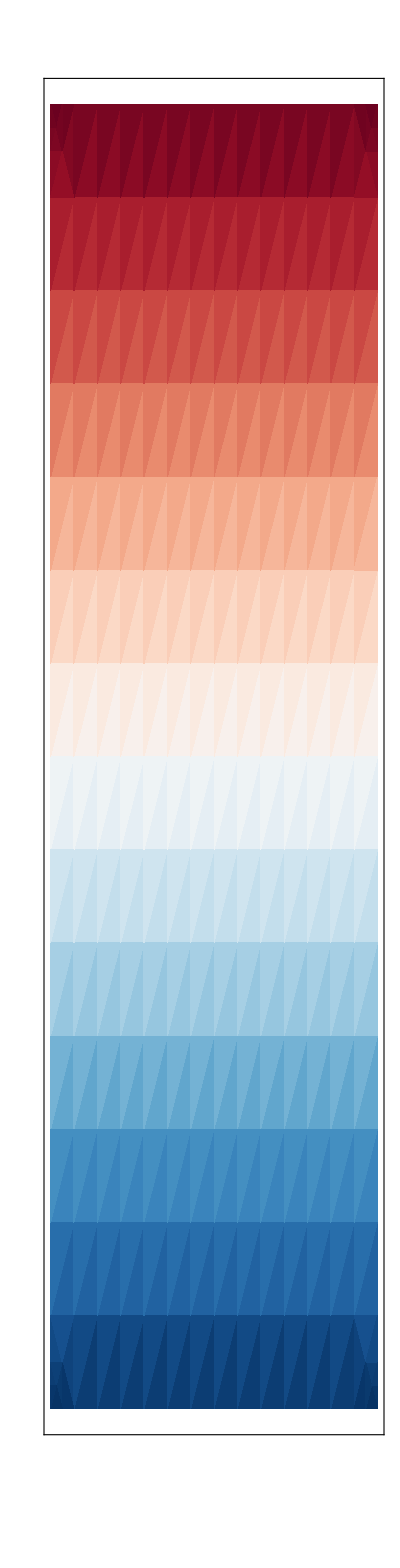

```mathematica
ClearAll[plotBarLegend];
plotBarLegend=DensityPlot[
y,
{x,-1,1},
{y,-1,1},

PlotRange->{{-1,1},{-1,1}},

ColorFunctionScaling->False,
ColorFunction->cf,

LabelStyle->texStyle14,

AspectRatio->15,

FrameTicks->{{None,All},{None,None}},

ImagePadding->{{2,31},{7,7}},
ImageSize->{Automatic,263}
]
```

## Plot function

```mathematica
ClearAll[plot];
plot[range_,points_,label_,time_,sigma_]:=Module[
{f},

f=exactGaussian[Sqrt[x^2+y^2],time,sigma];

DensityPlot[
f,

{x,-range,range},
{y,-range,range},

PlotRange->{Full,Full,{-1,1}},

PlotPoints->points,
MaxRecursion->6,

PlotTheme->"Scientific",
GridLines->None,

ColorFunctionScaling->False,
ColorFunction->cf,

LabelStyle->texStyle14,

ImageSize->{Automatic,300},
ImagePadding->{{40,8},{25,25}},
PlotRangePadding->None,

Exclusions->None,

Epilog->{
{
Text[Style[label,texStyle[16]],Scaled[{0.10,0.90}]]
}
}
]
];
```

## Plots

```mathematica
ClearAll[sigma,points,range];
sigma=1;

points=50;
range=10;

ClearAll[p1];
p1=plot[range,points,"A",0,sigma];

ClearAll[p2];
p2=plot[range,points,"B",1.5,sigma];

ClearAll[p3];
p3=plot[range,points,"C",3,sigma];

ClearAll[p];
p=Row[{p1,p2,p3,plotBarLegend}];

ClearAll[p1,p2,p3];
ClearAll[sigma,points,range];
```

## Export

```mathematica
Export["exact_gaussian_id_examples.png",p,ImageResolution->300,CompressionLevel->1];
Run["optipng -o2 exact_gaussian_id_examples.png"];
```